{J_0(x),J_1(x),J_2(x),J_3(x),J_4(x)}

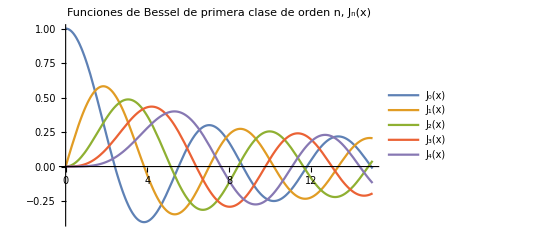

```mathematica
legends = Table[Row[{Subscript["J",n],"(x)"}],{n,0,4}]
Plot[Evaluate@Table[BesselJ[n,x],{n,0,4}],{x,0,15}, PlotLabel->Style["Funciones de Bessel de primera clase de orden n, J_n(x)", FontSize->16, Black],PlotLegends->legends,ImageSize->400]
```

{N_0(x),N_1(x),N_2(x),N_3(x),N_4(x)}

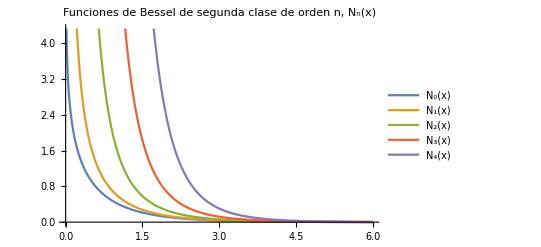

```mathematica
legends = Table[Row[{Subscript["N",n],"(x)"}],{n,0,4}]
Plot[Evaluate@Table[BesselK[n,x],{n,0,4}],{x,0,6}, PlotLabel->Style["Funciones de Bessel de segunda clase de orden n, N_n(x)", FontSize->16, Black],PlotLegends->legends,ImageSize->400]
```

```mathematica
Table[BesselJZero[μ,x]//N,{μ,0,4},{x,1,5}]//TableForm
```

2.40483 | 5.52008 | 8.65373 | 11.7915 | 14.9309
3.83171 | 7.01559 | 10.1735 | 13.3237 | 16.4706
5.13562 | 8.41724 | 11.6198 | 14.796 | 17.9598
6.38016 | 9.76102 | 13.0152 | 16.2235 | 19.4094
7.58834 | 11.0647 | 14.3725 | 17.616 | 20.8269

```mathematica
data=Flatten[Table[{n,k,N@BesselJZero[n,k]},{n,0,5},{k,1,5}],1]
```

{{0,1,2.40483},{0,2,5.52008},{0,3,8.65373},{0,4,11.7915},{0,5,14.9309},{1,1,3.83171},{1,2,7.01559},{1,3,10.1735},{1,4,13.3237},{1,5,16.4706},{2,1,5.13562},{2,2,8.41724},{2,3,11.6198},{2,4,14.796},{2,5,17.9598},{3,1,6.38016},{3,2,9.76102},{3,3,13.0152},{3,4,16.2235},{3,5,19.4094},{4,1,7.58834},{4,2,11.0647},{4,3,14.3725},{4,4,17.616},{4,5,20.8269},{5,1,8.77148},{5,2,12.3386},{5,3,15.7002},{5,4,18.9801},{5,5,22.2178}}